## Task 6

## Variant 3

```mathematica
h = 0.1
```

0.1

```mathematica
τ = 0.005
```

0.005

```mathematica
n = Round[1/h]
```

10

```mathematica
m = Round[0.015/τ]
```

3

```mathematica
index=0
```

0

```mathematica
xi=Table[Subscript[x, index++]->i,{i,0,1,h}]
```

{x_0→0.,x_1→0.1,x_2→0.2,x_3→0.3,x_4→0.4,x_5→0.5,x_6→0.6,x_7→0.7,x_8→0.8,x_9→0.9,x_10→1.}

```mathematica
index=0
```

0

```mathematica
ti=Table[Subscript[t, index++]->i,{i,0,1,τ}];
```

```mathematica
mat=Flatten@@{Table[(Subscript[u, i,j+1]-Subscript[u, i,j])/0.1==(Subscript[u, i+1,j]-2 Subscript[u, i,j]+Subscript[u, i-1,j])/0.1^2/.ti/.xi,{i,1,n-1},{j,0,m-1}]};
```

```mathematica
dop1=Table[Subscript[u, 0,i]==0/.ti,{i,1,m}];
```

```mathematica
dop2=Table[Subscript[u, n,i]==0/.ti,{i,1,m}];
```

```mathematica
dop3=Table[Subscript[u, i,0]==1/.xi,{i,0,n}];
```

```mathematica
dop3
```

{u_(0,0)==1,u_(1,0)==1,u_(2,0)==1,u_(3,0)==1,u_(4,0)==1,u_(5,0)==1,u_(6,0)==1,u_(7,0)==1,u_(8,0)==1,u_(9,0)==1,u_(10,0)==1}

```mathematica
AppendTo[mat,dop1];
```

```mathematica
AppendTo[mat,dop2];
```

```mathematica
AppendTo[mat,dop3];
```

```mathematica
sysMatrix=Flatten@@{mat};
```

```mathematica
sysMatrix=DeleteDuplicates[sysMatrix];
```

```mathematica
sysMatrix;
```

```mathematica
vars = Flatten[Table[Subscript[u, i,j],{i,0,n},{j,0,m}]];
```

```mathematica
vars;
```

```mathematica
solve = Solve[sysMatrix];
```

```mathematica
vars = {}
```

{}

```mathematica
solve;
```

```mathematica
For[i=0,i≤n,i++,
For[j=0,j≤m,j++,
vars=AppendTo[vars,{{Subscript[x, i]/.xi,Subscript[t, j]/.ti},Subscript[u, i,j]/.solve}]]]
```

```mathematica
DeleteCases
```

DeleteCases

```mathematica
vars
```

{{{0.,0.},{1.}},{{0.,0.005},{0.}},{{0.,0.01},{0.}},{{0.,0.015},{0.}},{{0.1,0.},{1.}},{{0.1,0.005},{1.}},{{0.1,0.01},{-9.}},{{0.1,0.015},{181.}},{{0.2,0.},{1.}},{{0.2,0.005},{1.}},{{0.2,0.01},{1.}},{{0.2,0.015},{-99.}},{{0.3,0.},{1.}},{{0.3,0.005},{1.}},{{0.3,0.01},{1.}},{{0.3,0.015},{1.}},{{0.4,0.},{1.}},{{0.4,0.005},{1.}},{{0.4,0.01},{1.}},{{0.4,0.015},{1.}},{{0.5,0.},{1.}},{{0.5,0.005},{1.}},{{0.5,0.01},{1.}},{{0.5,0.015},{1.}},{{0.6,0.},{1.}},{{0.6,0.005},{1.}},{{0.6,0.01},{1.}},{{0.6,0.015},{1.}},{{0.7,0.},{1.}},{{0.7,0.005},{1.}},{{0.7,0.01},{1.}},{{0.7,0.015},{1.}},{{0.8,0.},{1.}},{{0.8,0.005},{1.}},{{0.8,0.01},{1.}},{{0.8,0.015},{-99.}},{{0.9,0.},{1.}},{{0.9,0.005},{1.}},{{0.9,0.01},{-9.}},{{0.9,0.015},{181.}},{{1.,0.},{1.}},{{1.,0.005},{-2.09344×10^-16}},{{1.,0.01},{1.32694×10^-15}},{{1.,0.015},{0.}}}

```mathematica
tfixedVars=Select[vars,#⟦1,2⟧== 0.015&]
```

{{{0.,0.015},{0.}},{{0.1,0.015},{181.}},{{0.2,0.015},{-99.}},{{0.3,0.015},{1.}},{{0.4,0.015},{1.}},{{0.5,0.015},{1.}},{{0.6,0.015},{1.}},{{0.7,0.015},{1.}},{{0.8,0.015},{-99.}},{{0.9,0.015},{181.}},{{1.,0.015},{0.}}}

```mathematica
tfixedVarsEx=tfixedVars/.{{a_,b_},{c_}}-> {a,c}
```

{{0.,0.},{0.1,181.},{0.2,-99.},{0.3,1.},{0.4,1.},{0.5,1.},{0.6,1.},{0.7,1.},{0.8,-99.},{0.9,181.},{1.,0.}}

```mathematica
intfixed = Interpolation[tfixedVarsEx]
```

InterpolatingFunction[{{0., 1.}}, <>]

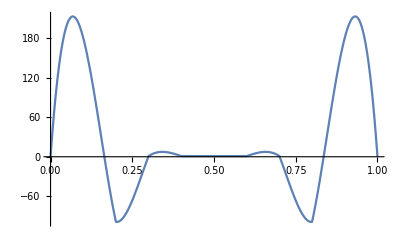

```mathematica
Plot[intfixed[x],{x,0.,1.}]
```

```mathematica
ifun = Interpolation[vars]
```

InterpolatingFunction[{{0., 1.}, {0., 0.015}}, <>]

```mathematica
Plot3D[ifun[x,t],{x,0,1},{t,0,0.015}]
```

-Graphics3D-